# Modèle 2.5 : Parasitoïde de larve αl = 0

## Présentation du modèle

```mathematica
ModeleComplet= {
U'[t] == q A[t] - δu U[t]- q A[t-τu] Exp[-τu δu],
L'[t] == q A[t-τu] Exp[-τu δu] -a L[t]P[t]-δl L[t] - q A[t-τu-τl]Exp[-τu δu]Exp[-τl δl] H[t],
M'[t] == q A[t-τu-τl]Exp[-τu δu]Exp[-τl δl] H[t]- δm M[t] - q A[t-τu-τl-τm]Exp[-τu δu] Exp[-τl δl] H[t-τm]Exp[-δm τm],
A'[t] ==  q A[t-τu-τl-τm]Exp[-τu δu] Exp[-τl δl] H[t-τm]Exp[-δm τm]-δa A[t],
J'[t] ==a L[t]P[t]-δj J[t]-a L[t-τj]P[t-τj] Exp[-δj τj],
P'[t] ==a L[t-τj]P[t-τj] Exp[-δj τj]-δp P[t],
H'[t] ==- H[t]a(P[t]-P[t-τl])
}
ModeleReduit = {
L'[t] == q A[t-τu] Exp[-τu δu] -a L[t]P[t]-δl L[t] - q A[t-τu-τl]Exp[-τu δu]Exp[-τl δl] H[t],
A'[t] ==  q A[t-τu-τl-τm]Exp[-τu δu] Exp[-τl δl] H[t-τm]Exp[-δm τm]-δa A[t],
P'[t] ==a L[t-τj]P[t-τj] Exp[-δj τj]-δp P[t],
H'[t] ==- H[t]a(P[t]-P[t-τl])
}
```

{U'[t]==q A[t]-ⅇ^(-δu τu) q A[t-τu]-δu U[t],L'[t]==ⅇ^(-δu τu) q A[t-τu]-ⅇ^(-δl τl-δu τu) q A[t-τl-τu] H[t]-δl L[t]-a L[t] P[t],M'[t]==ⅇ^(-δl τl-δu τu) q A[t-τl-τu] H[t]-ⅇ^(-δl τl-δm τm-δu τu) q A[t-τl-τm-τu] H[t-τm]-δm M[t],A'[t]==-δa A[t]+ⅇ^(-δl τl-δm τm-δu τu) q A[t-τl-τm-τu] H[t-τm],J'[t]==-δj J[t]+a L[t] P[t]-a ⅇ^(-δj τj) L[t-τj] P[t-τj],P'[t]==-δp P[t]+a ⅇ^(-δj τj) L[t-τj] P[t-τj],H'[t]==-a H[t] (P[t]-P[t-τl])}

{L'[t]==ⅇ^(-δu τu) q A[t-τu]-ⅇ^(-δl τl-δu τu) q A[t-τl-τu] H[t]-δl L[t]-a L[t] P[t],A'[t]==-δa A[t]+ⅇ^(-δl τl-δm τm-δu τu) q A[t-τl-τm-τu] H[t-τm],P'[t]==-δp P[t]+a ⅇ^(-δj τj) L[t-τj] P[t-τj],H'[t]==-a H[t] (P[t]-P[t-τl])}

## Étude analytique

## Points fixes

### Valeur à l’équilibre des taux de mortalité non fixe

```mathematica
HEqNnTri = Exp[-τl(δl+a Peq)];
```

### Modèle à l’équilibre

```mathematica
ModeleEq = {
0 == q Aeq Exp[-τu δu] -a Leq Peq-δl Leq - q Aeq Exp[-τu δu]Exp[-τl δl] Heq,
0 ==  q Aeq Exp[-τu δu] Exp[-τl δl] Heq Exp[-δm τm]-δa Aeq,
0 ==a Leq Peq  Exp[-δj τj]-δp Peq
};
MatrixForm[ModeleEq /.{Heq->HEqNnTri}]
```

(0==-a Leq Peq+Aeq ⅇ^(-δu τu) q-Aeq ⅇ^(-δl τl-(a Peq+δl) τl-δu τu) q-Leq δl
0==Aeq ⅇ^(-δl τl-(a Peq+δl) τl-δm τm-δu τu) q-Aeq δa
0==a ⅇ^(-δj τj) Leq Peq-Peq δp)

### Résolution globale

```mathematica
Solve[ModeleEq /.{Heq->HEqNnTri},{Leq,Aeq,Peq}]
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is InverseFunction[#1 ⅇ^#1&,1,1][-(Aeq ⅇ^(-(Aeq ⅇ^(-δu τu) q τl)/Leq-δu τu) q τl)/Leq] == 0.

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -δl τl+InverseFunction[#1 ⅇ^#1&,1,1][(ⅇ^(((a Leq Peq-Aeq Power[«2»] q+Leq δl) τl)/Leq) (a Leq Peq-Aeq ⅇ^(-δu τu) q+Leq δl) τl)/Leq] == 0.

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is InverseFunction[#1 ⅇ^#1&,1,1][-(Aeq ⅇ^(-(Aeq ⅇ^(-δu τu) q τl)/Leq-δu τu) q τl)/Leq] == 0.

General::stop: Further output of Solve::incnst will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Leq→(ⅇ^(δj τj) δp)/a,Aeq→0,Peq→-δl/a}}

### Résolution par parties

#### Recherche de Leq

```mathematica
LeqNnTri = Leq/.Solve[0==a ⅇ^(-δj τj) Leq Peq-Peq δp,Leq][[1]]
```

(ⅇ^(δj τj) δp)/a

#### Recherche de Peq

```mathematica
PeqNnTri = Peq/.Solve[0==Aeq ⅇ^(-δl τl-(a Peq+δl) τl-δm τm-δu τu) q-Aeq δa,Peq][[1]]
PeqNnTri = (-2 δl τl-δm τm-δu τu+Log[q/δa])/(a τl)
```

ConditionalExpression[(-2 δl τl-δm τm-δu τu+2 ⅈ π C[1]+Log[q/δa])/(a τl), C[1]∈ℤ]

(-2 δl τl-δm τm-δu τu+Log[q/δa])/(a τl)

#### Recherche de Aeq en fonction de Leq

```mathematica
AeqNnTri = Aeq/.Solve[0==-a Leq Peq+Aeq ⅇ^(-δu τu) q-Aeq ⅇ^(-δl τl-(a Peq+δl) τl-δu τu) q-Leq δl,Aeq][[1]]
AeqNnTri=AeqNnTri/.{Leq->LeqNnTri,Peq->PeqNnTri}
```

(ⅇ^(δl τl+(a Peq+δl) τl+δu τu) Leq (a Peq+δl))/((-1+ⅇ^(δl τl+(a Peq+δl) τl)) q)

(ⅇ^(δj τj+δl τl+δu τu+τl (δl+(-2 δl τl-δm τm-δu τu+Log[q/δa])/τl)) δp (δl+(-2 δl τl-δm τm-δu τu+Log[q/δa])/τl))/(a (-1+ⅇ^(δl τl+τl (δl+(-2 δl τl-δm τm-δu τu+Log[q/δa])/τl))) q)

### Vérification

```mathematica
FullSimplify[ModeleEq/.{Heq->HEqNnTri/.{Peq->PeqNnTri},Leq->LeqNnTri,Aeq->AeqNnTri/.{Leq->LeqNnTri,Peq->PeqNnTri},Peq->PeqNnTri}]
```

{True,True,True}

On est bon !!!!

### Condition d’existence des points fixes

```mathematica
Solve[0==PeqNnTri,q]
Solve[0==PeqNnTri,δu]/.{δl->0,δa->0.1,δm->0,τu->4,τl->16,τm->8}
Solve[0==PeqNnTri,δl]/.{δu->0,δa->0.1,δm->0,τu->4,τl->16,τm->8}
Solve[0==PeqNnTri,δm]/.{δl->0,δa->0.1,δu->0,τu->4,τl->16,τm->8}
Solve[0==PeqNnTri,δa]/.{δl->0,δu->0,δm->0,τu->4,τl->16,τm->8}
Solve[0==PeqNnTri,δa]
```

{{q→ConditionalExpression[ⅇ^(2 δl τl+δm τm+δu τu) δa, -π<Im[2 δl τl+δm τm+δu τu]≤π]}}

{{δu→1/4 Log[10. q]}}

{{δl→1/32 Log[10. q]}}

{{δm→1/8 Log[10. q]}}

{{δa→q}}

{{δa→ConditionalExpression[ⅇ^(-2 δl τl-δm τm-δu τu) q, -π<Im[2 δl τl+δm τm+δu τu]≤π]}}

### Conclusion Point Fixe

Possibilité de trouver les points fixes et leur condition d’existance

## Linéarisation

```mathematica
ModeleLineaire = {
nL'[t] == q nA[t-τu] Exp[-τu δu] -a nL[t]Peq-a Leq nP[t]-δl nL[t] - q nA[t-τu-τl]Exp[-τu δu]Exp[-τl δl] Heq- q Aeq Exp[-τu δu]Exp[-τl δl] nH[t],
nA'[t] ==  q nA[t-τu-τl-τm]Exp[-τu δu] Exp[-τl δl] Heq Exp[-δm τm]+q Aeq Exp[-τu δu] Exp[-τl δl] nH[t-τm]Exp[-δm τm]-δa nA[t],
nP'[t] ==a nL[t-τj]Peq Exp[-δj τj]+a Leq nP[t-τj] Exp[-δj τj]-δp nP[t],
nH'[t] ==- Heq a(nP[t]-nP[t-τl])
}
```

{nL'[t]==ⅇ^(-δu τu) q nA[t-τu]-ⅇ^(-δl τl-δu τu) Heq q nA[t-τl-τu]-Aeq ⅇ^(-δl τl-δu τu) q nH[t]-a Peq nL[t]-δl nL[t]-a Leq nP[t],nA'[t]==-δa nA[t]+ⅇ^(-δl τl-δm τm-δu τu) Heq q nA[t-τl-τm-τu]+Aeq ⅇ^(-δl τl-δm τm-δu τu) q nH[t-τm],nP'[t]==a ⅇ^(-δj τj) Peq nL[t-τj]-δp nP[t]+a ⅇ^(-δj τj) Leq nP[t-τj],nH'[t]==-a Heq (nP[t]-nP[t-τl])}

## Transformation de Laplace

```mathematica
ModeleLaplace = {
-s L[s] + q A[s]Exp[-s τu] Exp[-τu δu] -a L[s]Peq-a Leq P[s]-δl L[s] - q A[s-τu-τl]Exp[-s τu-s τl]Exp[-τu δu]Exp[-τl δl] Heq- q Aeq Exp[-τu δu]Exp[-τl δl] H[s],
-s A[s] + q A[s]Exp[-s τu-s τl-s τm]Exp[-τu δu] Exp[-τl δl] Heq Exp[-δm τm]+q Aeq Exp[-τu δu] Exp[-τl δl] H[s] Exp[-s τm]Exp[-δm τm]-δa A[s],
-s P[s] +a L[s]Exp[-s τj]Peq Exp[-δj τj]+a Leq P[s]Exp[-s τj] Exp[-δj τj]-δp P[s],
-s H[s] - Heq a(P[s]-P[s]Exp[-s τl])
}
```

{ⅇ^(-s τu-δu τu) q A[s]-ⅇ^(-s τl-δl τl-s τu-δu τu) Heq q A[s-τl-τu]-Aeq ⅇ^(-δl τl-δu τu) q H[s]-a Peq L[s]-s L[s]-δl L[s]-a Leq P[s],ⅇ^(-s τl-δl τl-s τm-δm τm-s τu-δu τu) Heq q A[s]-s A[s]-δa A[s]+Aeq ⅇ^(-δl τl-s τm-δm τm-δu τu) q H[s],a ⅇ^(-s τj-δj τj) Peq L[s]+a ⅇ^(-s τj-δj τj) Leq P[s]-s P[s]-δp P[s],-s H[s]-a Heq (P[s]-ⅇ^(-s τl) P[s])}

## Jacobienne

```mathematica
JacobienneGeneral =  D[ModeleLaplace,{{L[s],A[s],P[s], H[s]}}];
MatrixForm[JacobienneGeneral]
```

(-a Peq-s-δl | ⅇ^(-s τu-δu τu) q | -a Leq | -Aeq ⅇ^(-δl τl-δu τu) q
0 | ⅇ^(-s τl-δl τl-s τm-δm τm-s τu-δu τu) Heq q-s-δa | 0 | Aeq ⅇ^(-δl τl-s τm-δm τm-δu τu) q
a ⅇ^(-s τj-δj τj) Peq | 0 | a ⅇ^(-s τj-δj τj) Leq-s-δp | 0
0 | 0 | -a (1-ⅇ^(-s τl)) Heq | -s)

```mathematica
JacobienneEqNnTri = FullSimplify[JacobienneGeneral/.{Leq->LeqNnTri,Aeq->AeqNnTri,Peq->PeqNnTri, Heq->(HEqNnTri/.Peq ->PeqNnTri)}]
```

{{(-s τl+δl τl+δm τm+δu τu-Log[q/δa])/τl,ⅇ^(-((s+δu) τu)) q,-ⅇ^(δj τj) δp,(ⅇ^(δj τj-δl τl) q δp (δl τl+δm τm+δu τu-Log[q/δa]))/(a (q-ⅇ^(δm τm+δu τu) δa) τl)},{0,-s+(-1+ⅇ^(-s (τl+τm+τu))) δa,0,(ⅇ^(δj τj-δl τl-(s+δm) τm) q δp (δl τl+δm τm+δu τu-Log[q/δa]))/(a (-q+ⅇ^(δm τm+δu τu) δa) τl)},{-(ⅇ^(-((s+δj) τj)) (2 δl τl+δm τm+δu τu-Log[q/δa]))/τl,0,-s+(-1+ⅇ^(-s τj)) δp,0},{0,0,-(a ⅇ^(-s τl+δl τl+δm τm+δu τu) (-1+ⅇ^(s τl)) δa)/q,-s}}

## *Stabilité*

### Point Fixe trivial

### Point Fixe non trivial

## Équation caractéristique et sa transformation

```mathematica
EquationCaracteristique = Det[JacobienneEqNnTri]
```

-s (-s+(-1+ⅇ^(-s (τl+τm+τu))) δa) (((-s+(-1+ⅇ^(-s τj)) δp) (-s τl+δl τl+δm τm+δu τu-Log[q/δa]))/τl-(ⅇ^(δj τj-(s+δj) τj) δp (2 δl τl+δm τm+δu τu-Log[q/δa]))/τl)-(a ⅇ^(-((s+δj) τj)-s τl+δl τl+δm τm+δu τu) (-1+ⅇ^(s τl)) δa ((ⅇ^(δj τj-δl τl-(s+δm) τm-(s+δu) τu) q^2 δp (δl τl+δm τm+δu τu-Log[q/δa]))/(a (-q+ⅇ^(δm τm+δu τu) δa) τl)-(ⅇ^(δj τj-δl τl) q (-s+(-1+ⅇ^(-s (τl+τm+τu))) δa) δp (δl τl+δm τm+δu τu-Log[q/δa]))/(a (q-ⅇ^(δm τm+δu τu) δa) τl)) (2 δl τl+δm τm+δu τu-Log[q/δa]))/(q τl)

### Focus sur les solution avec Réel Nul

```mathematica
EquationCaracteristiqueI =EquationCaracteristique /.{s->I x}
```

-ⅈ x (-ⅈ x+(-1+ⅇ^(-ⅈ x (τl+τm+τu))) δa) (((-ⅈ x+(-1+ⅇ^(-ⅈ x τj)) δp) (-ⅈ x τl+δl τl+δm τm+δu τu-Log[q/δa]))/τl-(ⅇ^(δj τj-(ⅈ x+δj) τj) δp (2 δl τl+δm τm+δu τu-Log[q/δa]))/τl)-1/(q τl)a ⅇ^(-((ⅈ x+δj) τj)-ⅈ x τl+δl τl+δm τm+δu τu) (-1+ⅇ^(ⅈ x τl)) δa ((ⅇ^(δj τj-δl τl-(ⅈ x+δm) τm-(ⅈ x+δu) τu) q^2 δp (δl τl+δm τm+δu τu-Log[q/δa]))/(a (-q+ⅇ^(δm τm+δu τu) δa) τl)-(ⅇ^(δj τj-δl τl) q (-ⅈ x+(-1+ⅇ^(-ⅈ x (τl+τm+τu))) δa) δp (δl τl+δm τm+δu τu-Log[q/δa]))/(a (q-ⅇ^(δm τm+δu τu) δa) τl)) (2 δl τl+δm τm+δu τu-Log[q/δa])

```mathematica
eqCaraRe = ComplexExpand[Re[EquationCaracteristiqueI]];
eqCaraIm = ComplexExpand[Im[EquationCaracteristiqueI]];
```

## Étude numérique

## Import et paramètres

### Paramètres

```mathematica
τuN=4.72;τlN=16;τmN=8.92;δuN=0.0432;δlN=0.0048;δmN=0.0150;δpN=1;δaN=1/12.2;δjN=δlN;τjN=τlN;aN=1;
```

### Gamme de δa et q

```mathematica
δaMin =0.001; δaMax = 1; δaPas = 0.001;
qMin =0; qMax = 10; qPas = 0.01;

δaRangeInv=Range[δaMax,δaMin,-δaPas];
δaRange=Range[δaMin,δaMax,δaPas];
qRange=Range[qMin,qMax,qPas];
```

## Limite de stabilité en fonction de δa et q

### Fixation des paramètres

```mathematica
eqCaraReEq = eqCaraRe /.{τu ->τuN,τl ->τlN,τm ->τmN,δu ->δuN,δl->δlN,δm->δmN,δp->δpN,δj->δjN,τj->τjN,a->aN};
eqCaraImEq = eqCaraIm /.{τu ->τuN,τl ->τlN,τm ->τmN,δu ->δuN,δl->δlN,δm->δmN,δp->δpN,δj->δjN,τj->τjN,a->aN};
```

### Recherche de valeur d’initialisation du FindRoot

```mathematica
FindRoot[{eqCaraReEq/.{δa->1},eqCaraImEq/.{δa->1}},{x,1.5},{q,2}]
FindRoot[{eqCaraReEq/.{δa->0.001},eqCaraImEq/.{δa->0.001}},{x,0.2},{q,0.2}]
```

{x→1.55129,q→1.40163}

{x→1.98795×10^-21,q→-0.144965}

### Création des Courbes

```mathematica
CourbeLimiteCompJulia1 = {}  ;  CourbeLimiteCompJulia2 = {}  ;  
ClearAll[qtempo, xtempo,δa,q,root,  x]
qtempo =5;
xtempo =0.2;
Do [
root = FindRoot[{eqCaraReEq,eqCaraImEq},{x,xtempo},{q,qtempo}];
qtempo = q/.root ;
xtempo = x/.root ;
AppendTo[CourbeLimiteCompJulia1,{qtempo,δa}];
,{δa,δaMax,δaMin,-δaPas}] 

ClearAll[qtempo, xtempo,δa,q,root,  x]
qtempo =1;
xtempo =0.1 ;
Do [
root = FindRoot[{eqCaraReEq,eqCaraImEq},{x,xtempo},{q,qtempo}];
qtempo = q/.root ;
xtempo = x/.root ;
AppendTo[CourbeLimiteCompJulia2,{qtempo,δa}];
,{δa,δaMax,δaMin,-δaPas}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {x,q} = {0.203081,3.91137×10^12}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

### Affichage des résultats

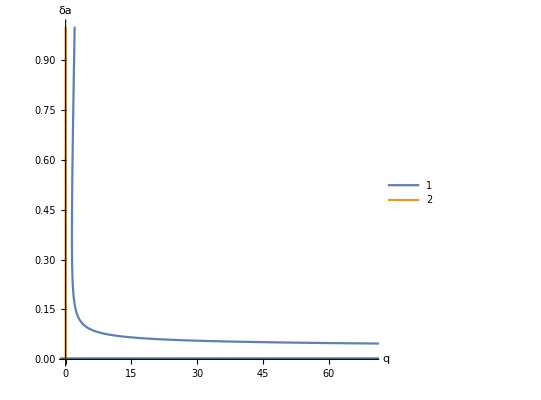

```mathematica
ListLinePlot[{CourbeLimiteCompJulia1,CourbeLimiteCompJulia2},
Axes->True,
AxesLabel -> {"q","δa"},
PlotLegends -> Automatic,
Ticks->Automatic,
AxesOrigin->{0,0},
AspectRatio-> 1,
PlotRange->{{0,70},{0,1}}
]
```

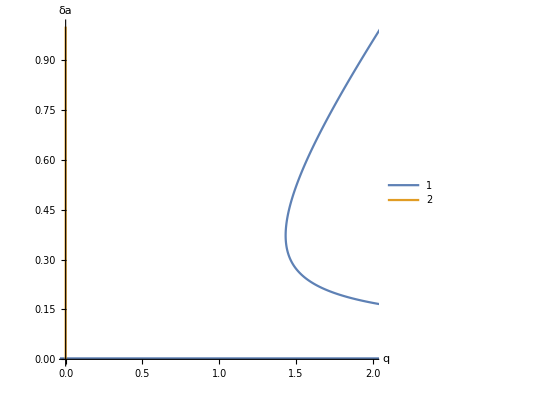

```mathematica
ListLinePlot[{CourbeLimiteCompJulia1,CourbeLimiteCompJulia2},
Axes->True,
AxesLabel -> {"q","δa"},
PlotLegends -> Automatic,
Ticks->Automatic,
AxesOrigin->{0,0},
AspectRatio-> 1,
PlotRange->{{0,2},{0,1}}
]
```

## Limite de stabilité en fonction de δu et q

### Fixation des paramètres

```mathematica
eqCaraReEq = eqCaraRe /.{τu ->τuN,τl ->τlN,τm ->τmN,δa ->δaN,δl->δlN,δm->δmN,δp->δpN,δj->δjN,τj->τjN,a->aN};
eqCaraImEq = eqCaraIm /.{τu ->τuN,τl ->τlN,τm ->τmN,δa ->δaN,δl->δlN,δm->δmN,δp->δpN,δj->δjN,τj->τjN,a->aN};
```

### Recherche de valeur d’initialisation du FindRoot

```mathematica
FindRoot[{eqCaraReEq/.{δu->1},eqCaraImEq/.{δu->1}},{x,16},{q,60}]
FindRoot[{eqCaraReEq/.{δu->0.001},eqCaraImEq/.{δu->0.001}},{x,2},{q,2}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→16.0003,q→64.8526}

{x→0.692929,q→0.0000785503}

### Création des Courbes

```mathematica
CourbeLimiteCompJulia1 = {}  ;  CourbeLimiteCompJulia2 = {}  ;  
ClearAll[qtempo, xtempo,δu,q,root,  x]
qtempo =64.85255874360234;
xtempo =16.00032387373853;
Do [
root = FindRoot[{eqCaraReEq,eqCaraImEq},{x,xtempo},{q,qtempo}];
qtempo = q/.root ;
xtempo = x/.root ;
AppendTo[CourbeLimiteCompJulia1,{qtempo,δu}];
,{δu,δaMax,δaMin,-δaPas}]
```

```mathematica
ClearAll[qtempo, xtempo,δu,q,root,  x]
qtempo =0.00007855027598529099;
xtempo =0.6929287303725669 ;
Do [
root = FindRoot[{eqCaraReEq,eqCaraImEq},{x,xtempo},{q,qtempo}];
qtempo = q/.root ;
xtempo = x/.root ;
AppendTo[CourbeLimiteCompJulia2,{qtempo,δu}];
,{δu,δaMax,δaMin,-δaPas}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

### Affichage des résultats

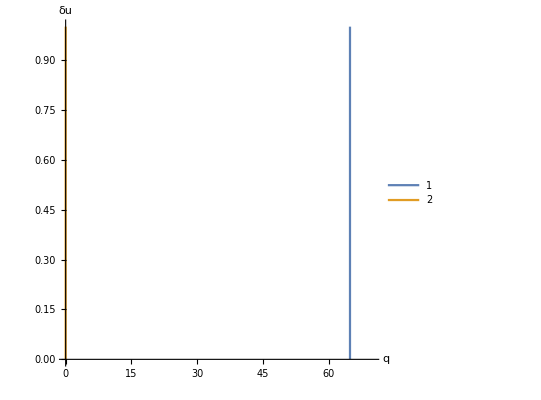

```mathematica
ListLinePlot[{CourbeLimiteCompJulia1,CourbeLimiteCompJulia2},
Axes->True,
AxesLabel -> {"q","δu"},
PlotLegends -> Automatic,
Ticks->Automatic,
AxesOrigin->{0,0},
AspectRatio-> 1,
PlotRange->{{0,70},{0,1}}
]
```

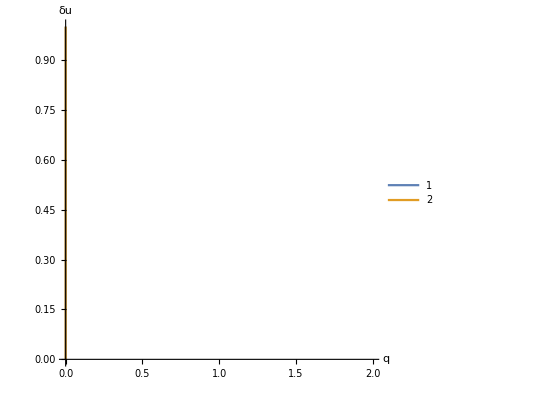

```mathematica
ListLinePlot[{CourbeLimiteCompJulia1,CourbeLimiteCompJulia2},
Axes->True,
AxesLabel -> {"q","δu"},
PlotLegends -> Automatic,
Ticks->Automatic,
AxesOrigin->{0,0},
AspectRatio-> 1,
PlotRange->{{0,2},{0,1}}
]
```

## Comparaison de dynamique avec Julia

### Paramétrisation

### Recherche de valeur d’initialisation du FindRoot

### Création des Courbes

### Affichage des résultats

## Dynamiques

## Comparaison de dynamique avec Julia

```mathematica
tmax = 10;qN=20;
```

```mathematica
(*Définir les fonctions par morceaux*)Lpiecewise[t_]:=Piecewise[{{0,t<0}},L[t]]
Apiecewise[t_]:=Piecewise[{{0,t<0}},A[t]]
Ppiecewise[t_]:=Piecewise[{{0,t<0}},P[t]]
Hpiecewise[t_]:=Piecewise[{{-τlN*ΔlN,t<0}},H[t]]

(*Résoudre les équations différentielles*)
solN=NDSolve[{ModeleReduit/. {δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δa->δaN,δj->δjN,τj->τjN,δp->δpN,a->aN,L[t]->Lpiecewise[t],A[t]->Apiecewise[t],P[t]->Ppiecewise[t],H[t]->Hpiecewise[t]},(*Conditions initiales à t=0*)L[0]==0,A[0]==1,P[0]==0.1,H[0]==-τlN*(aN*0.1+δlN)},{L,A,P,H},{t,0,tmax},Method->{"ExplicitRungeKutta","DifferenceOrder"->4},MaxSteps->Infinity,AccuracyGoal->10,PrecisionGoal->10];

(*Tracer les solutions*)
Plot[Evaluate[{Lpiecewise[t],Apiecewise[t],Ppiecewise[t]}/. solN],{t,0,tmax},PlotLegends->{"L","A","P"},AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```

```mathematica
solN=NDSolve[{ModeleReduit/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δa->δaN,δj->δjN,τj->τjN,δp->δpN,a->aN},
L[0]==0,A[0]==1,P[0]==0.1,H[0]==-τlN*(aN*0.1+δlN),L[t/;t<0]==0,A[t/;t<0]==0,P[t/;t<0]==0, H[t/;t<0]==-τlN*δlN},{L,A,P,H},{t,0,tmax},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4},
MaxSteps->Infinity,AccuracyGoal->10,PrecisionGoal->10];
Plot[Evaluate[{L[t],A[t],P[t]}/. solN],{t,0,tmax},PlotLegends->{"L","A","P"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of t.

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

NDSolve::ndnco: The number of constraints (8) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (4).

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of t.

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{{L'[t]==16.3108 A[«1»]-15.105 A[«1»] H[«1»]-0.0048 L[«1»]-L[«1»] P[«1»],A'[t]==-0.0819672 A[«1»]+13.2134 A[«1»] H[«1»],P'[t]==0.926075 L[«1»] P[«1»]-P[«1»],H'[t]==-H[t] (Times[«2»]+P[«1»])},L[0]==0,A[0]==1,P[0]==0.1,H[0]==-1.6768,L[t/;t<0]==0,A[t/;t<0]==0,P[t/;t<0]==0,H[t/;t<0]==-0.0768},{L,A,P,H},{t,0,10},Method→{ExplicitRungeKutta,DifferenceOrder→4},MaxSteps→∞,AccuracyGoal→10,PrecisionGoal→10]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{L'[0.000204286]==16.3108 A[«1»]-15.105 A[«1»] H[«1»]-0.0048 L[«1»]-L[«1»] P[«1»],A'[0.000204286]==-0.0819672 A[«1»]+13.2134 A[«1»] H[«1»],P'[0.000204286]==0.926075 L[«1»] P[«1»]-P[«1»],H'[0.000204286]==-H[0.000204286] (Times[«2»]+P[«1»])},L[0]==0,A[0]==1,P[0]==0.1,H[0]==-1.6768,L[0.000204286/;t<0]==0,A[0.000204286/;t<0]==0,P[0.000204286/;t<0]==0,H[0.000204286/;t<0]==-0.0768},{L,A,P,H},{0.000204286,0,10},Method→{ExplicitRungeKutta,DifferenceOrder→4},MaxSteps→∞,AccuracyGoal→10,PrecisionGoal→10]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{L'[0.000204286]==16.3108 A[«1»]-15.105 A[«1»] H[«1»]-0.0048 L[«1»]-1. L[«1»] P[«1»],A'[0.000204286]==-0.0819672 A[«1»]+13.2134 A[«1»] H[«1»],P'[0.000204286]==0.926075 L[«1»] P[«1»]-1. P[«1»],H'[0.000204286]==-1. H[0.000204286] (Times[«2»]+P[«1»])},L[0.]==0.,A[0.]==1.,P[0.]==0.1,H[0.]==-1.6768,L[0.000204286/;t<0.]==0.,A[0.000204286/;t<0.]==0.,P[0.000204286/;t<0.]==0.,H[0.000204286/;t<0.]==-0.0768},{L,A,P,H},{0.000204286,0.,10.},Method→{ExplicitRungeKutta,DifferenceOrder→4.},MaxSteps→∞,AccuracyGoal→10.,PrecisionGoal→10.]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.204286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-

$Aborted

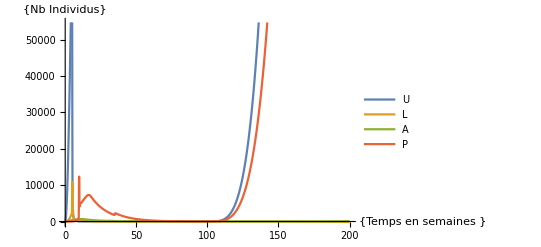

```mathematica
solN=NDSolve[{ModeleQuentin/.{δu -> δuN,δl -> δlN, δm -> δmN,τu -> τuN, τl -> τlN, τm-> τmN,q->qN,δa->δaN,αl->αlN,δj->δjN,τj->τjN,δp->δpN,a->aN},U[t/;t<=0]==1,L[t/;t<=0]==1,A[t/;t<=0]==1,P[t/;t<=0]==1, Hc[t/;t<=0]==0,Hp[t/;t<=0]==0},{U,L,A,P,Hc,Hp},{t,0,tmax},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4},
MaxSteps->Infinity,AccuracyGoal->10,PrecisionGoal->10];
Plot[Evaluate[{U[t],L[t],A[t],P[t]}/. solN],{t,0,tmax},PlotLegends->{"U","L","A","P"}, AxesLabel->{{"Temps en semaines "},{"Nb Individus"}}]
```